# Efficient Bayesian Regularization by Kalman Folding

Brian Beckman
4 June 2019

## Abstract

Maximum a-posteriori (MAP) is the go-to method for Bayesian linear regression. It regularizes (avoids over-fitting) by incorporating a-priori beliefs. The contributions of this paper are functional Kalman folding (KAL) and renormalized recurrent least squares (RRLS), propose as robust, scalable, and flexible alternatives to MAP. Robust because KAL and RRLS avoid matrix inversion, unlike MAP. Scalable because KAL and RRLS process data one observation at a time, avoiding MAP’s storage of whole data sets. Flexible because KAL and RRLS apply to lazy and asynchronous streams without modification, unlike MAP.

KAL and RRLS are equally Bayesian to MAP because they are recurrent and must be bootstrapped with a-priori beliefs. This fact is not often noticed because KAL and RRLS are Bayesian by construction; they are not merely mechanisations of non-Bayesian Maximum-Likelihood Estimation, as is sometimes assumed. Although Kalman filtering, invented in the 1960’s, predates the vigorous growth of Bayesian methods in the 1990’s, it is actually based on exactly the same Bayesian premises, not on frequentist premises as is sometimes assumed.

We show, by numerical examples, that KAL produces the same results as RRLS and as MAP for appropriate choices of a-priori covariances. MAP’s estimates, though not its covariances, are invariant when MAP's hyperparameters are swapped and inverted. After that transformation, the MAP equations strongly resemble the equations of Kalman filtering, suggesting a conjecture that, in general, not merely for the numerical examples presented, the recurrent, thus flexible, form of MAP is actually KAL and RRLS.

We close with another example: recurrent KAL and RRLS for a non-linear model: Padé approximants. A transformation to linear form opens them to Kalman filtering.

## Introduction

Linear systems appear everywhere: machine learning, control, quantum and classical dynamics, and robotics. We usually approximate non-linear systems with linear models because non-linear systems are often intractable. We must study linear systems and linear models because they are everywhere and because they are usually necessary for solving non-linear problems.

Linear regression is the standard technique for estimating coefficients or parameters of a linear model from observed data. Over-fitting is a hazard. Linear models, as their order (number of parameters) nears or exceeds the number of data points, follow the data too well, “wiggle too much.” Such wiggling limits smoothness: it is difficult to predict values in-between the given data points. Such wiggling also limits generalization (extrapolation): it is difficult to predict points outside the “ball” that contains the given data points.

Regularization is the usual fix for over-fitting. In the Bayesian maximum a-posteriori (MAP) method, we effect regularization with a-priori belief hyperparameters α and β; α=1/σ_ξ^2 and β=1/σ_ζ^2 are, respectively, the reciprocal variance of an a-priori estimate ξ of the unknown model parameters and the reciprocal variance of an a-priori estimate of the predicted observations ζ. In the jargon of Kalman filtering, these variances are, respectively, process noise and observation noise (Kalman filtering has non-Bayesian jargon for Bayesian notions because Kalman filtering predated the Bayesian explosion of the 1990’s). 

We show here, numerically, that MAP produces the same estimate ξ when α and β are swapped and inverted. After that transformation, the MAP equations strongly resemble the equations of Kalman filtering. Noticing that resemblance led us to the investigations behind this paper. These variances are concrete and we can estimate or learn them directly from experiment. In post-processing, we must produce covariances of the estimates and of the predicted observations from nominal α=1/σ_ξ^2 and β=1/σ_ζ^2 as specified in the original formulation of MAP. 

We further noticed that some well known presentations of backpropagation in neural networks by policy gradient are yet-another-application of Kalman filtering, just, this time, on a dual space of gradient co-vectors (row-vectors) as opposed to the usual column vectors of parameters of linear models.

KAL and recurrent least squared (RLS) scale better than MAP (see Kalman folding). MAP is a Bayesian modification of the normal equations of maximum-likelihood (MLE) regression. MLE and and MAP encourage explicit computation over whole data sets stored in memory. There is no obvious way to convert MLE and MAP into recurrences, let alone to extend them to lazy sequences or to asynchronous streams. KAL and RLS, however, process data one observation at a time. They are overtly recurrent, thus independent of the manner of data delivery, asynchronous or not, and they avoid storage and multiplication of large matrices. KAL and RLS, therefore, have natural expressions as functional folds, finding easy expression in contemporary programming languages.

## Motivating Review

First, we apply maximum-likelihood estimation (MLE) to a problem of order two: estimating the slope m and intercept b of the best-fit line function z(x)=m x+b to noisy data (x_i,z_i). 

Although the function-being-fitted is a line, it is a non-linear function of the independent variable x. The most general linear function of x is a constant m times x. Such a function has one parameter, m. The function z(x)=m x+b has two parameters; it is a two-parameter affine function of x. It is a linear function of the parameters m and b, but not of the independent variable x. 

More generally, think of z(x)=m x+b as a linear combination of potentially non-linear basis functions of x. In the case of z(x)=m x+b, there are two basis functions. The first basis function is z_m(x)=x, the identity function of x. The linear combination m z_m(x)=m x happens, accidentally, to be linear in the independent variable x. Do not be distracted or confused by that linearity; it is not the linearity we’re looking for. The linearity of m z_m(x)=m x in the parameter m is the interesting linearity. The second basis function, z_b(x)=1, is non-linear in x, but the linear combination b z_b(x) is likewise linear in the parameter b. 

The idea of adding up linear combinations of non-linear functions extends linear methods to sophisticated and highly non-linear models. Seeing z(x)=m x+b as z(x)=m z_m(x)+b z_b(x) makes it easy to imagine adding more terms. For example, a Fourier series ∑_(k=0)^∞ a_k e^(i ω_k x) with many terms is linear in the amplitudes a_k, but each harmonic basis function e^(i ω_k x) basis function is non-linear in x. Likewise, a linear combination of non-linear Bessel’s functions best approximates an arbitrary vibratory configuration of a circular drumhead. A linear combination of non-linear Legendre polynomials best approximates an arbitrary lumpy spheroid. The claim “best approximated by” comes from Sturm-Liouville theory, which finds “best” basis functions as eigenfunctions of self-adjoint differential operators. 

We bring up these facts to emphasize the linear methods MLE, MAP, KAL, RLS, RRLS are powerful tools for estimating sophisticated models, linear in the parameters but non-linear in the independent variables.

We compute MLE in four independent but equivalent ways:

(WBI) with Wolfram built-in functions

(CNE) directly through the classic normal equations

(LPI) using the Moore-Penrose left pseudoinverse

(SLS) sidestepping the inverse by solving a linear system

These methods of MLE yield exactly and numerically the same results for this example.

Problem Statement

Find best-fitting parameters m (slope) and b (intercept), where z(x)=m x+b, given known, noisy data (z_1,z_2,…,z_k) and (x_1,x_2,…,x_k). Best-fitting means minimizing mean squared error.

Write this system as a matrix equation and remember the symbols

Ζ (observations; known, concrete, numerical)

A (partials, Jacobian of the observation model z(x)=m x+b with respect to the parameters m and b; known, concrete, numerical)

Ξ=(m, b)ᵀ (model, state; unknown abstract, symbolic parameters to be estimated).

Rows of data Ζ and partials A come in matched pairs.

Ζ_(Ν×1)  =  (z_1
z_2
⋮
z_Ν)   =   (x_1 | 1
x_2 | 1
⋮ | ⋮
x_Ν | 1)  ·  (m_unknown
b_unknown)   +  noise   
=  A_(Ν×2)·Ξ_(2×1)  +  samples of NormalDistribution[0,σ_Ζ]

Ground Truth

Fake some data by (1) sampling a line specified by ground truth m_GT and b_GT, then (2) adding Gaussian noise. Run the faked data through the four estimation procedures WBI, CNE, LPI, SLS, and see how close the estimated m_estimated and b_estimated come to ground truth. The model is of order M=2 in this first example. There are N observed scalar data, thus Ζ is a column vector of order N, and N=119l in this first example.

In real-world applications, we rarely have ground truth. Its purpose here is to baseline or calibrate the four estimation procedures WBI, CNE, LPI, SLS. Note and remember the ground-truth values m_GT=0.5, b_GT=-1/3.

```mathematica
ClearAll[groundTruth,m,b];
groundTruth={m,b}={0.5,-1./3.};
```

Partials

The partials A are a (order-Ν) column vector of co-vectors (order-Μ row vectors; linear transformation functions of Μ-vectors). Each co-vector row is the Jacobian gradient 1-form of A·Ξ with respect to Ξ, evaluated at specific values of Ξ from the data. It is best to view gradients as 1-forms, always co-vectors.

```mathematica
ClearAll[nData,min,max];
nData=119;min=-1.;max=3.;
ClearAll[partials];
partials=Array[{#,1.0}&,nData,{min,max}];
Short[partials,3]
```

{{-1.,1.},{-0.966102,1.},«115»,{2.9661,1.},{3.,1.}}

Faked Observations Ζ

Define a global variable, data, used in later derivations and demonstrations. Assume that the observations have unbiased (zero-mean) Gaussian white noise with variance σ_Ζ=0.65.

```mathematica
ClearAll[fake];
fake[n_,σ_,A_,{m_,b_}]:=
Table[
RandomVariate[NormalDistribution[0,σ]]+A⟦i⟧.{m,b},
{i,n}];
```

```mathematica
ClearAll[data,noiseσ];
noiseσ=0.65;
data=fake[nData,noiseσ,partials,groundTruth];
Short[data,3]
```

{-3.71491,-1.30242,«115»,0.73975,0.265457}

Wolfram Built-In

The Wolfram built-in LinearModelFit computes an MLE for Ξ=(m
b). For one particular run, the estimated (m_estimated
b_estimated)=(0.5266
-0.3798) are reasonably close to the ground truth (m
b)=(0.5
-1/3).

```mathematica
ClearAll[model];
model=LinearModelFit[{partials⟦All,1⟧,data}ᵀ,x,x];
Normal[model]
```

-0.369837+0.526635 x

Un-comment the following line to see everything Wolfram has to say about this MLE (it’s a lot of data).

```mathematica
(*Association[(#->model[#])&/@model["Properties"]]*)
```

The most important attribute of the model is its covariance matrix. We come back to it below.

```mathematica
model["CovarianceMatrix"]//MatrixForm
```

(0.0072146 | -0.00306231
-0.00306231 | 0.00306231)

The following plot shows that Wolfram does a pragmatically acceptable job of estimating the parameters m and b. We have 119 data and two parameters to estimate, so over-fitting is not an issue because the number of data greatly exceeds the number of parameters.

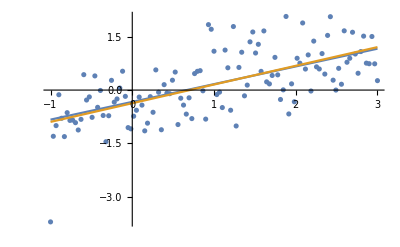

```mathematica
Show[ListPlot[{partials⟦All,1⟧,data}ᵀ],
Plot[{m x+b,model[x]},{x,min,max}]]
```

Normal Equations

Solve equation 1 for a value of Ξ that minimizes sum-squared error J(Ξ)=^def(Ζ-A·Ξ)ᵀls·(Ζ-A·Ξ). That is the same as maximizing the likelihood p ( Z|Ξ ) of the data Z given the parameters Ξ, a fact that gives the name Maximum-Likelihood Estimation to the MLE method. Because the noise 𝒩(0,σ) is unbiased, the solution is exactly what one gets from naive algebra:  Aᵀ·A is square; when it is invertible:

(Aᵀ·A)^-1·Aᵀ·Z  =  Ξ

That gives numerically the same answer as Wolfram’s built-in:

```mathematica
Inverse[partialsᵀ.partials].partialsᵀ.data
```

{0.526635,-0.369837}

### Moore-Penrose PseudoInverse

The matrix (Aᵀ·A)^-1·Aᵀ is the Moore-Penrose left pseudoinverse. Wolfram has a built-in for it. We get exactly the same answer as above:

```mathematica
PseudoInverse[partials].data
```

{0.526635,-0.369837}

### Avoiding Inversion

Avoid the inverse via LinearSolve.

```mathematica
LinearSolve[partialsᵀ.partials,partialsᵀ].data
```

{0.526635,-0.369837}

### Do Not Use the Normal Equations

(Aᵀ·A)^-1·Aᵀ·Ζ is a nasty computation: in memory usage (big matrices), in time (matrix multiplication), and in numerical risk (inverse). How to avoid these hazards? Find a recurrence relation.

## Recurrence

Fold the following recurrence over Ζ and A:

ξ←(Λ+[aᵀ·a])^-1·([aᵀ·ζ]+[Λ·ξ])
Λ←(Λ+[aᵀ·a])

where

ξ is the current estimate of Ξ

a and ζ are matched rows of A and Ζ

Λ accumulates Aᵀ·A

### Derivation Sketch

Derive the recurrence as follows: Treat the estimate-so-far,

ξ_(so-far)=^def(Aᵀ·A)^-1·Aᵀ·Ζ_(so-far)

as just one more observation. Let Λ, the information matrix, be:

Λ=A_(so-far)ᵀ·A_(so-far)

The scalar performance or squared error of the known estimate, ξ_(so-far), is

J(ξ)  =  (Ζ_(so-far)-A_(so-far)·ξ)ᵀ·(Ζ_(so-far)-A_(so-far)·ξ)  =  (ξ-ξ_(so-far))ᵀ·Λ·(ξ-ξ_(so-far))

where ξ is the unknown true parameter vector, Ζ_(so-far) is the (known, concrete) column vector of all observations so-far. Adding a new observation, ζ, and its corresponding partial row co-vector a, increases the error J(ξ) by (ζ-a·ξ)ᵀ·(ζ-a·ξ). Minimize the new total error with respect to ξ to find the recurrence (set the derivative of J with respect to ξ to zero and solve the resulting system). ■

RLS introduces an a-priori estimate ξ_0 and an a-priori covariance, the inverse of the a-priori information matrix Λ_0. RLS is therefore Bayesian by construction---incorporating a-priori data and uncertainty forces Bayes’s theorem to obtain [TODO: proof]. 

When renormalized with an a-priori covariance for the observations ζ, the recurrence relation in equation 3 is equivalent to KAL and empirically, numerically equivalent to MAP. We show the renormalization procedure below. Rigorous proof of theoretical equivalence to MAP awaits future work.

### Numerical Demonstration

Bootstrap the recurrence with ad-hoc, a-priori values ξ_0=(0 | 0)ᵀ and Λ_0=((10^-6 | 0)(0 | 10^-6)).

```mathematica
ClearAll[update];
update[{ξ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{Inverse[Π].(aᵀ.ζ+ Λ.ξ),Π}];

MatrixForm/@
({({{mBar}, {bBar}}),Π}=
Fold[update,{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.526635
-0.369837),(280.356 | 119.
119. | 119.)}

The estimates mBar and bBar are, numerically, the same as we got from Wolfram’s built-in. For this example, the choice of ξ_0 and Λ_0 had negligible effect.

### Structural Notes

The highlighted mappings of List over the data and partials convert them into column vectors.

### Memory and Time Efficiency

The required memory for the recurrence is O(Μ), where Μ is the order of the model = the number of parameters to estimate = the length of Ξ = the length of each row of A. The recurrence does not depend on the number Ν of data items. The recurrence accumulates data one observation at a time, and thus consumes O(Ν) in time. Contrast with the normal equations, which multiply at ~O(Ν^3) and invert at ~O(Μ^3), i.e., at much greater time cost.

### Check the A-Priori

The final value of Λ (called Π in the code, a returned value), is A_full ᵀ·A_full+Λ_0. Check that the difference between Π and A_full ᵀ·A_full is Λ_0, the a-priori covariance:

```mathematica
Π-partialsᵀ.partials
```

{{1.×10^-6,0.},{0.,1.×10^-6}}

### Covariance of the Estimate

The covariance of this estimate Ξ is ((n-1)/(n-2))*Variance [ Ζ-A·Ξ ]*Λ^-1 except for a small contribution from the a-priori information Λ_0. The correction factor ((n-1)/(n-2)) is a generalization of Bessel’s correction. The 2 in (n-2) in the denominator of Bessel’s correction is the number of parameters estimated, also called degrees of freedom (see VAN DE GEER, Least Squares Estimation, Volume 2, pp. 1041–1045, in Encyclopedia of Statistics in Behavioral Science, Eds. Brian S. Everitt & David C. Howell, Wiley, 2005). The denominator of the correction, in general, is n-p, where n is the number of data and p is the number of parameters being estimated.

```mathematica
Inverse[partialsᵀ.partials]*(nData-1)/(nData-2)*Variance[data-partials.{mBar,bBar}]//MatrixForm
```

(0.00306231 | -0.00306231
-0.00306231 | 0.0072146)

```mathematica
(cov$=Inverse[Π]*(nData-1)/(nData-2)*Variance[data-partials.{mBar,bBar}])//MatrixForm
```

(0.00306231 | -0.00306231
-0.00306231 | 0.0072146)

(Naming convention: suffixed dollar signs denote undisciplined, ad-hoc, global variables like cov$. Assign and reassign such variables without care, but they may have different values in different places in the notebook. They are for intermediate calculations only.)

This is the same covariance matrix that Wolfram’s LinearModel reports:

```mathematica
Reverse@(Reverse/@model["CovarianceMatrix"])//MatrixForm
```

(0.00306231 | -0.00306231
-0.00306231 | 0.0072146)

### Covariance of the Prediction

If we view the two parameters, m and b, as random variables, then the predicted value z at every input point x is a linear combination of those random variables. That linear combination is, in turn, a random variable with variance x^2 σ_m^2+σ_b^2+E[(b-E[b])(m x-E[m x])], when z is a scalar. The following plot shows the one-sigma band around the model in blue, ground truth in green. MAP adds an a-priori covariance of the observations, and we renormalize the recurrent form to match covariance of the predictions to MAP exactly. We explain such renormalization below.

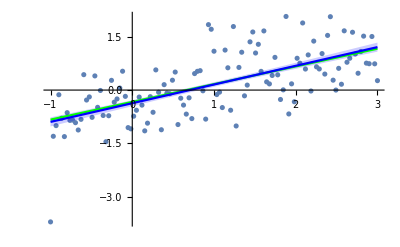

```mathematica
Module[{row,diagonalTerm,offDiagonalTerm,Σ},
row[x_]:={{x,1.}};
diagonalTerm[x_]:=Map[Dot[Diagonal[cov$],#]&,#^2&/@row[x]];
offDiagonalTerm[x_]:=MapThread[Dot,{row[x].cov$,row[x]}];
Σ[x_]:=Sqrt[(row[x].cov$.row[x]ᵀ)⟦1,1⟧];
With[{points={partials⟦All,1⟧,data}ᵀ},
Show[ListPlot[{points}],
Plot[{m x+b,
model[x],
model[x]+Σ[x],
model[x]-Σ[x]},{x,min,max},
PlotStyle->{
Green,Blue,
{Thin,{Opacity[0],Blue}},
{Thin,{Opacity[0],Blue}}},
Filling->{2->{3},2->{4}}]]]]
```

Don’t Invert That Matrix

See https://www.johndcook.com/blog/2010/01/19/dont-invert-that-matrix/ 

In general, replace any occurrence of A^-1·B or Inverse[A].B with LinearSolve[A,B] for arbitrary square matrix A and arbitrary matrix B. Almost all programming languages and toolkits support an efficient and robust analogue to Wolfram’s LinearSolve.

```mathematica
ClearAll[update];
update[{ξ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{LinearSolve[Π,(aᵀ.ζ+Λ.ξ)],Π}];

MatrixForm/@({({{mBar}, {bBar}}),Π}=
Fold[update,{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.526635
-0.369837),(280.356 | 119.
119. | 119.)}

Because this example is small, Inverse has no obvious numerical issues. In general, matrices in linear regression are ill-conditioned, and one will spend a lot of time and storage inverting them, only to get useless results.

Speed Under Stress

```mathematica
ClearAll[experiment];
experiment[n_]:=
With[{min=-1,max=3,noiseσ=1.0},
Module[{A,zs,time={0,0},zc,Ac,stream},
A=Array[{#,1.0}&,n,{min,max}];
zs=fake[n,noiseσ,A,groundTruth];
zc=List/@zs;
Ac=List/@A;
stream={zc,Ac}ᵀ;
time⟦1⟧=AbsoluteTiming[Inverse[Aᵀ.A].Aᵀ.zs];
time⟦2⟧=AbsoluteTiming[
Fold[
update,{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
stream]];
time   ]];
```

```mathematica
experiment[10000]//MatrixForm
```

(0.008743 | {0.503389,-0.338863}
0.172629 | {{{0.503389},{-0.338863}},{{23336.,10000.},{10000.,10000.}}})

Interim Conclusions

We have eliminated memory bloat by processing updates one observation at a time, each with its paired partial. We reduce computation time and numerical risk by solving a linear system instead of inverting a matrix. We avoid multiplication of O(Ν) matrices, which is of approximately O(Ν^3) time. We still have work to do with observation covariances.

## SIDEBAR: Estimating 1-Forms (Gradients)

In linear algebra, vectors are columns, i.e., n×1 matrices, and co-vectors are rows, i.e., 1×n matrices (see Vector Calculus, Linear Algebra, and Differential Forms, A Unified Approach by John H. Hubbard and Barbara Burke Hubbard).

When the model — the thing we are estimating — is a co-vector (row-vector), e.g., a 1-form, we have the dual (co-, transposed) problem to the one above. This situation arises in reinforcement learning by policy gradient. In that case, the observations Ω and the model Γ are co-vectors with elements ω and γ instead of vectors ζ and ξ. The co-partials Θ (replacing A) are now a covector of column vectors θ. The observation equation is Ω=Γ·Θ and the error-so-far is (x-γ)·Λ·(x-γ)ᵀ, where Λ=Θ_(so-far)·Θ_(so-far)ᵀ. We don’t change the name of Λ because it is symmetric, equal to its dual (transpose). Adding a new observation ω introduces new error (ω-x·θ)·(ω-x·θ)ᵀ. Minimizing the total error yields

γ←([γ·Λ]+[ω·θ ᵀ]).(Λ+[θ·θ ᵀ] )^-1
Λ←(Λ+[θ·θ ᵀ] )

straight transposes of equation 3. LinearSolve operates on the transposed right-hand side of the recurrence. Transpose the solution to get the recurrence. Apply the resulting dual model to the transpose of the original data:

```mathematica
ClearAll[coUpdate];
coUpdate[{γ_,Λ_},{ω_,θ_}]:=
With[{Π=(Λ+θ.θᵀ)},
{LinearSolve[Π,Λ.γᵀ+θ.ωᵀ]ᵀ,Π}];
```

```mathematica
MatrixForm/@Fold[coUpdate,
{({{0, 0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@List/@data,Transpose/@List/@partials}ᵀ]
```

{(0.526635 | -0.369837),(280.356 | 119.
119. | 119.)}

This also awaits renormalization, however, the new equations will be obvious.

Application of the Dual Problem

The finite-difference method of policy-gradient machine learning provides an example of this dual problem (see http://www.scholarpedia.org/article/Policy_gradient_methods). 

Imagine a scalar function J(θ) of a column K-vector θ_(K×1). Estimate its gradient co-vector ∇_θ J, given a batch of ℐ of random increments ΔΘ_(K×ℐ), from the linear system ∇_θ J·ΔΘ=Δ J. As an observation model; ∇_θ J takes the role of the model whose state parameters Γ we want to estimate; ΔΘ takes the role of the partials of the model w.r.t. those parameters; and Δ J takes the role of measured data. Let Δ J_(ℐ×1) be a batch of observed increments to J and let ΔΘ_(K×ℐ) be a matrix of ℐ corresponding column-vector random increments to the input vectors θ_(K×1). The Moore-Penrose right pseudoinverse RPI=^def ΔΘ_(K×ℐ)^ᵀ·(ΔΘ_(K×ℐ)·ΔΘ_(K×ℐ)^ᵀ)^-1  solves ∇_θ J_(ℐ×1)·ΔΘ_(K×ℐ)=Δ J_(ℐ×1) to yield ∇ J_(ℐ×1)≈Δ J_(ℐ×1)·RPI. 

(EXERCISE) Instead of the pseudoinverse, which is large, slow, and risky, use the co-update recurrence of equation 7, or its later renormalization, for this problem.

## Regularization By A-Priori

Chris Bishop’s Pattern Recognition and Machine Learning has an extended example of fitting higher-order polynomials, linear in their coefficients, starting in section 1.1. The higher the order of the polynomial, the more MLE over-fits. Bishop presents MAP regularization as a cure for this over-fitting. We point out that KAL and RLS already regularize, by construction. In this section, we relate their regularization to MAP’s.

To bootstrap recurrences, KAL and RLS each require an a-priori estimate of the unknown parameters and an a-priori uncertainty of that estimate. RLS takes the a-priori uncertainty as an information matrix. KAL takes the a-priori uncertainty as a covariance matrix, inverse of the information matrix. Bishop also computes the information matrix as S^-1, though he does not name it so. KAL additionally requires an estimate of observation noise, which arises in real problems and is estimated out-of-band. We show how to renormalize RLS withl observation noise to produce results equivalent to KAL and MAP.

Reproducing Bishop’s Example

### Bishop’s Training Set

First, create a sequence of Ν=10 inputs — for a training set, equally spaced in [0,1].

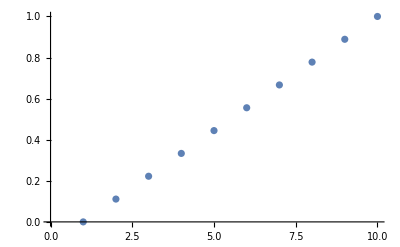

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[Ν_]:=Array[Identity,Ν,{0.,1.}];
ListPlot[bishopTrainingSetX[10]]
```

Bishop’s ground truth is a single cycle of a sine wave. Add noise to a sample taken at the inputs of the training set above. Bishop doesn’t state his observation noise, but I guess σ_z=σ_t=0.30 to create a fake data set that resembles Bishop’s qualitatively.

Wolfram’s built-in NormalDistribution takes the standard deviation as its second argument, not the variance. Bishop’s notation for normal distribution takes variance as second argument, so beware.

```mathematica
ClearAll[bishopTrainingSetY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopTrainingSetY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Take a sample of the outputs and assign it the names bts for bishopTrainingSet. It is not his actual training set, which I did not find in print, just my simulation.

```mathematica
ClearAll[bishopTrainingSet,bts,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopTrainingSetY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bts=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

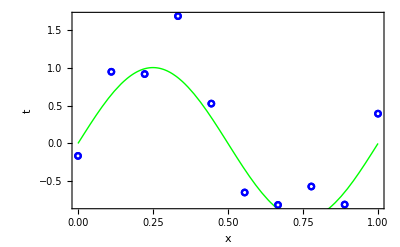

```mathematica
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

### Partials: Gradients of the Unknown Parameters

Write a function for partials. Quietly map the indeterminate 0^0 to 1. Test it symbolically.

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
MatrixForm@partialsFn[6,{Subscript[x, 1],Subscript[x, 2],Subscript[x, Μ]}]
```

(1 | x_1 | x_1^2 | x_1^3 | x_1^4 | x_1^5 | x_1^6
1 | x_2 | x_2^2 | x_2^3 | x_2^4 | x_2^5 | x_2^6
1 | x_Μ | x_Μ^2 | x_Μ^3 | x_Μ^4 | x_Μ^5 | x_Μ^6)

### The Observation Equations

Confer Bishop’s equation 3.3, page 138. He writes the parameters-to-estimate as w and he writes the observation equation as

y(x, w)=∑_(j=0)^Μ w_j ϕ_j (x)

(bias incorporated as coefficient w_0 of the 0^th basis function). This is predictive: you give me concrete inputs x, parameters w, and I’ll give you a predicted observation y in terms of Μ+1 basis functions ϕ corresponding to the Μ+1 unknown parameters. For polynomial basis functions, the number of parameters is one more than the order Μ of the polynomials. The basis functions can be anything, however: wavelets, Fourier components, Chebyshev polynomials, etc.

Bishop transposes w into a co-vector (without explanation) and writes

y(x, w)=wᵀϕ (x)

where ϕ (x) is an (Μ+1)-dimensional column-vector of basis functions, each a transpose of one row of our partials matrix A. Better: always think of partials or gradients as values of differential forms, thus co-vectors (row vectors or covariant vectors, see https://en.wikipedia.org/wiki/Covariance_and_contravariance _of _vectors, https://math.stackexchange.com/questions/1172022, and https://math.stackexchange.com/questions/54355). 

To find best-fit values for w, rows of the partials matrix A are the co-vector gradients of y with respect to w. We prefer to write

observations as height-N column-vector Ζ_Ν with elements ζ_(j ∈ [ 1 ..Ν ])

the model or unknown parameters, an (Μ+1)-dimensional column-vector Ξ_((Μ+1)×1) with elements ξ_(i ∈ [ 0 ..Μ ])

partials matrix as A_(N×(Μ+1))

Bishop calls our partials matrix the design matrix in his equation 3.16, page 142, consisting of values of the basis functions at the concrete inputs x_(n ∈ [1..N]). Bishop must work in the dual of our formulation. 

We prefer to write the co-vector rows of the design matrix as polynomial basis functions evaluated at the input points x_(n ∈ [1..Ν]):

Z  =  A·Ξ  =  (ζ_0
ζ_1
⋮
ζ_Ν)  =   (1=x_1^0 | x_1 | x_1^2 | ⋯ | x_1^M
1=x_2^0 | x_2 | x_2^2 | ⋯ | x_2^M
⋮ | ⋮ |   | ⋱ | ⋮
1=x_N^0 | x_N | x_N^2 | ⋯ | x_N^M)  ·  (ξ_0
ξ_1
⋮
ξ_Μ)  +  noise

then packed up into rows of the A matrix.

Z  =  A·Ξ  =  (ζ_0
ζ_1
⋮
ζ_Ν)  =   (A_(1×(Μ+1))(x_1)
A_(1×(Μ+1))(x_2)
⋮
A_(1×(Μ+1))(x_Ν))_(Ν×(Μ+1))  ·  (ξ_0
ξ_1
⋮
ξ_Μ)  +  noise

### MLE: The Normal Equations

Mechanize the normal equations for comparison purposes; we expect them to over-fit.

```mathematica
ClearAll[mleFit];
mleFit[Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
PseudoInverse[partialsFn[Μ,xs]].ys];
mleFit[3,bts]
```

{-0.190652,14.3733,-40.8215,27.0474}

A convenience function:

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
```

The normal equations as a symbolic polynomial follows. Notice we can increase the order beyond the number of data, creating an underdetermined system. This is not typical in real-world data processing. Usually the number of data exceed the order and the system is overdetermined. The pseudoinverse is agnostic to the distinction.

```mathematica
ClearAll[x];
Manipulate[
symbolicPowers[x,Μ].mleFit[Μ,bts],
{{Μ,3,"polynomial order Μ"},0,16,1,Appearance->{"Labeled"}}]
```

### RLS: Recurrent Least Squares

Regularize RLS by its a-priori estimate of the unknown parameters and by its a-priori information matrix. Slide the slider below. Check that, once the minimum info becomes too large, the Λ matrix becomes ill-conditioned: pink warning message appear from the Wolfram kernel, and the solution becomes numerically suspect. In the rest of this paper, we eliminate these error message by applying Wolfram’s Quiet because we notice, empirically, that ill-conditioning of the information matrix does not seem to be harmful in this example. However, such ill-conditioning is a serious problem in practice and must be tracked and managed with methods out-of-scope in this paper.

```mathematica
ClearAll[rlsFit];
rlsFit[σ2Λ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2Λ*IdentityMatrix[Μ+1]},
Fold[update,{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ]]];

Manipulate[
rlsFit[10^-logσ2Λ][3,bts]⟦1⟧//MatrixForm,
{{logσ2Λ,9.034},0,16,Appearance->"Labeled"}]
```

### KAL: Foldable Kalman Filter

The foldable Kalman filter (KAL) follows below. This version has only the update phase of a typical Kalman filter because the parameters-to-estimate are constant and therefore there is no predict phase.

Note the P_Ζ parameter, the first in the definition of kalmanUpdate. This is the covariance matrix of the observation noise. It is a constant throughout the folding run of the filter. That is why we lambda-lift it into its own function slot; kalmanUpdate, called with some concrete value of P_Ζ, yields a foldable lambda-function. Initialize the fold with a-priori estimate ξ_0 and covariance P_0 and run the fold over a sequence of observation-and-partial-co-vector pairs {ζ,a}. Fold is useful for all kinds of Bayesian methods, which require an a-priori, abstract zero of the monoid (https://github.com/rebcabin/DontFear/blob/master/Decoding.pdf).

```mathematica
ClearAll[kalmanUpdate,kalFit];
kalmanUpdate[PΖ_][{ξ_,P_},{ζ_,a_}]:=
Module[{D,KT,K,L},
D=PΖ+a.P.aᵀ;
KT=LinearSolve[D,a.P];K=KTᵀ;
L=IdentityMatrix[Length[P]]-K.a;
{ξ+K.(ζ-a.ξ),L.P}];

kalFit[σζ2_,σξ2_][order_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,order+1],
P0=σξ2*IdentityMatrix[order+1]},
Fold[kalmanUpdate[σζ2*IdentityMatrix[1]],
{ξ0,P0},
{List/@ys,List/@partialsFn[order,xs]}ᵀ]]];
```

### See All Three

The following interactive demonstration shows mleFit (normal equations), rlsFit (recurrent least squares), and kalFit (Kalman folding) on Bishop’s training set.

When the a-priori information matrix in RLS is 10^-6, and when the a-priori covariance of the a-priori estimate in KAL is 10^6, both KAL and RLS produce regularized fits. In contrast, the MLE over-fits a 9^th-order polynomial by interpolating (going through) every data point. A 9^th-order polynomial fits ten data points exactly. The normal equations are neither overdetermined nor underdetermined at order nine, but are exactly solvable.

Increasing -logΛ decreases the (magnitude of the) a-priori information matrix in RLS, lending less Bayesian belief in the a-priori estimate ξ_0 of the unknown parameters ξ. Increasing logσξ2 increases the a-priori covariance σ_ξ_0^2 of the estimate in KAL, also decreasing belief in the a-priori estimate ξ_0. As Λ decreases and σ_ξ_0^2 increases, RLS and KAL, respectively, eventually over-fit the data completely and align with MLE. Later, we show that MAP similarly over-fits as belief in the a-priori decreases. 

Run the polynomial order up to nine, then -logΛ and logσξ2 all the way to the right, to their maximum values, to see the effect described in the last paragraph.

```mathematica
Manipulate[
Module[{x},(* gensym: fresh variable name *)
With[{
terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧},
With[{
recurrent=Quiet@rlsFit[10^-logΛ0][Μ,bts],
normal=mleFit[Μ,bts],
kalman=kalFit[bishopFakeSigma^2,10^logσξ2][Μ,bts]},
With[{
rlsFn={terms}.recurrent⟦1⟧,
mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{
{Grid[{{
Button["RESET",(Μ=9;logΛ0=3;logσξ2=3)&],
Control[{{rlsQ,True,"RLS"},{True,False}}],
Control[{{kalQ,True,"KAL"},{True,False}}],
Control[{{mleQ,True,"MLE"},{True,False}}]}}]},{Control[{{Μ,9,"polynomial order"},0,16,1,Appearance->{"Labeled"}}]},{Control[{{logΛ0,3,"-log a-priori info (RLS)"},0,16,Appearance->"Labeled"}]},{Control[{{logσξ2,3,"log a-priori cov (KAL)"},0,16,Appearance->"Labeled"}]}}]]
```

Renormalizing RLS

When the observation noise Ζ is unity, KAL coincides with RLS. In the demonstration below, a-priori information Λ in RLS is set always to be the inverse of KAL’s a-priori estimate covariance P; KAL and RLS will have the same belief in the a-priori estimate of the unknown parameters. Vary the observation noise independently to see KAL and RLS coincide when the observation noise is unity (its log is zero).

As observation noise decreases, the solutions believe the observations more and RLS and KAL over-fit. As a-priori covariance decreases, RLS and KAL believe the a-priori estimates more and the solution regularizes.

```mathematica
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧},
With[{rls=Quiet@rlsFit[10^(-2logσξ)][Μ,bts],
kalman=kalFit[10^(2logσζ),10^(2logσξ)][Μ,bts]},
With[{rlsFn={terms}.rls⟦1⟧,
kalFn={terms}.kalman⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];
If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{{Grid[{{Button["RESET",(logσζ=0.0;logσξ=1.5;Μ=9)&],
Control[{{rlsQ,True,"RLS"},{True,False}}],
Control[{{kalQ,True,"KAL"},{True,False}}]}}],""},{Control[{{Μ,9,"polynomial order"},0,16,1,Appearance->{"Labeled"}}],""},{Control[{{logσξ,1.5,"log √P (KAL) = (-log √Λ) (RLS) "},-3,8,Appearance->"Labeled"}]},{Control[{{logσζ,0.0,"log √Ζ (KAL)"},-6,3,Appearance->"Labeled"}]}}]]
```

### Add Observation Noise to RLS

RLS, so far, is normalized to unit observation noise. How to modify RLS to account for non-unit observation noise? 

Scale (each row of) the partials by the inverse of the observation standard deviation, represented below by a matrix square root of the observation covariance P_Ζ. Finally, rescale the final estimate (not the final covariance) by a matrix built from the inverse observation standard deviation because the recurrent normal equations, which incrementally build (P_Ζ^-1·Aᵀ·A·P_Ζ^-T)^-1·P_Ζ^-1·Aᵀ·Ζ, have one too many factors of P_Ζ.

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];

Manipulate[
With[{ξ0=({{0}, {0}}),Λ0=({{1.0*^-6, 0}, {0, 1.0*^-6}}),m=MatrixForm,
inputs={List/@data⟦1;;n⟧,List/@partials⟦1;;n⟧}ᵀ},
Module[{ξrr,ξr,ξk,Πrr,Πr,Πk},
({ξrr,Πrr}=Fold[rlsUpdate[σ IdentityMatrix[1]],
{ξ0,Λ0},inputs]);
({ξr,Πr}=Fold[update,{ξ0,Λ0},inputs]);
({ξk,Πk}=Fold[kalmanUpdate[σ^2],{ξ0,Inverse@Λ0},inputs]);
Grid[{
{"","Renormalized RLS","RLS","KAL"},
{"Estimate",m[(IdentityMatrix[2]/σ).ξrr],m@ξr,m@ξk},
{"Info Mat",m@Πrr,m[Πr/σ^2],m[Inverse@Πk]},
{"Mat Diffs",
m@Chop[Abs[Πrr-Πr/σ^2],10^-9],
m@Chop[Abs[Inverse@Πk-Πr/σ^2],10^-9],
m@Chop[Abs[Inverse@Πk-Πrr],10^-9]}},Frame->{All,{True,True,None}}]]],
{{n,3},3,nData,1,Appearance->"Labeled"},
{{σ,10},-100,100,Appearance->"Labeled"}]
```

### RLS beats KAL

KAL and renormalized RLS (RRLS) are mathematically equivalent. Operationally, KAL subtracts matrices to recur covariance of the estimates. That subtraction is exposed to catastrophic cancelation. RLS only adds to the information matrix, so is exposed only to ill-conditioning, which is empirically less severe than catastrophic cancelation. We show this below.

## Regularization and MAP

Bishop reports β=11.111… and α=0.005 in his figure 1.17 (page 32) and in equations 1.70 through 1.72 (page 31), which look suspiciously like the equations for Kalman filtering. Bishop’s matrix S looks like D^-1 in kalmanUpdate above. Let’s reproduce MAP via KAL and RLS.

Bishop’s MAP

### The MAP Equations

Bishop’s equations 1.70 through 1.72 are reproduced here. The dimensions of the identity matrix in S is Μ+1, where Μ is the order of the polynomial model, one more than Μ to account for the leading bias term. It turns out that Bishop’s S^-1 is exactly the information matrix of RLS, as we see in the section on Covariance of the Prediction, below.

m(x)  =  β ϕ (x)ᵀ·S·∑_(n=1)^N ϕ (x_n)t_n

s^2(x)  =  β^-1+ϕ (x)ᵀ·S·ϕ (x)

S^-1  =^def  α I_(Μ+1)+β∑_(n=1)^N ϕ (x_n)·ϕ (x_n)ᵀ

Here are some links between Bishop’s formulation and ours, without derivation.

∑_(n=1)^N ϕ (x_n)t_n=Aᵀ·Ζ

lim_(α→0) ( β^-1 S^-1)=Aᵀ·A

### Φ Vectors

Bishop’s ϕ (x_n) is an (Μ+1)-dimensional column vector of the powers of the n^th input x_n. These powers are the basis functions of a polynomial model for the curve. ϕ (x_n) is the dual (transpose) of one row of our partials matrix A. 

As written, Bishop’s equations are non-recurrent, requiring all data t_n and ϕ (x_n) in memory. Plus, as written, they require inverting matrix S. They thus suffer from the operational ills of the normal equations.

```mathematica
ClearAll[ϕ];
ϕ[Μ_][xn_]:=Quiet@Table[xn^i,{i,0,Μ}]/.{Indeterminate->1};
MatrixForm/@ϕ[3]/@List/@bts⟦1⟧
```

{(1
0.
0.
0.),(1.
0.111111
0.0123457
0.00137174),(1.
0.222222
0.0493827
0.0109739),(1.
0.333333
0.111111
0.037037),(1.
0.444444
0.197531
0.0877915),(1.
0.555556
0.308642
0.171468),(1.
0.666667
0.444444
0.296296),(1.
0.777778
0.604938
0.470508),(1.
0.888889
0.790123
0.702332),(1.
1.
1.
1.)}

### S Inverse

Bishop’s equation 1.72.

```mathematica
ClearAll[sInv,α,β];
sInv[α_,β_,cs_,Μ_]:=
With[{Ν=Length[cs]},
α IdentityMatrix[Μ+1]+β Sum[cs⟦i⟧.cs⟦i⟧ᵀ,{i,Ν}]];
```

### MAP Mean

Bishop’s equation 1.70.

```mathematica
ClearAll[mapMean];
mapMean[α_,β_,x_,cs_,ts_,Μ_]:=
With[{Ν=Length@cs},
{β*ϕ[Μ][x]}.(* row of partials *)
LinearSolve[(* vector of coefficients *)
sInv[α,β,cs,Μ],
ts.cs]]⟦1,1⟧;
```

### a-priori Variances α and β

Bishop defines β=1/σ_ζ^2, where σ_ζ is the standard deviation, from the model, of the predicted observation ζ. The predicted observation ζ is the value of the model on an arbitrary input ξ. Similarly, Bishop defines α=1/σ_ξ^2, where σ_ξ is the standard deviation of the a-priori distribution of the unknown parameter estimate ξ.

#### Mean Is Invariant Under “Swap and Invert”

We observe, numerically, that Bishop's equations for the estimate (mean) match KAL and RLS when β is σ_ξ^2 and when α=σ_ζ^2, that is, the covariances are swapped and inverted. In the demonstration below, expect m_1 to equal m_2. We present the other quantities to support future analysis. We leave non-empirical, rigorous proof to the future. The demonstration below algebraically verifies the proposition that m_1=m_2, at least up to order 4. Above order 4, the following becomes too hard Mathematica.

```mathematica
ClearAll[x,α,β,chopQ];
DynamicModule[{chopQ=False},
Manipulate[With[{cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧,
pf=If[chopQ,Chop,Identity]@*FullSimplify},
With[{m1=mapMean[α,β,x,cs,ts,Μ],
m2=mapMean[1/β,1/α,x,cs,ts,Μ],
si1=sInv[α,β,cs,Μ],
si2=sInv[1/β,1/α,cs,Μ]},
Grid[({{"m1", pf@m1}, {"m2", pf@m2}, {"m1-m2", pf[m1-m2]}, {"si1", pf@si1}, {"si2", pf@si2}, {"si1-si2", pf[si1-si2]}}),Frame->All]]],
Column[{Row[{Button["UN-CHOP",chopQ=False],"        ",
Button["CHOP",chopQ=True]}],
Control[{{Μ,2,"order Μ"},0,4,1,Appearance->{"Open","Labeled"}}]}]]]
```

The other two combinations, where β=1/σ_ζ^2 and α=σ_ζ^2 or β=σ_ξ^2 and α=1/σ_ξ^2, are not correct. Intuitively, these two combinations do not contain full information about the a-priori beliefs in both ζ and ξ, so we do not expect them to be correct. This fact can be demonstrated numerically.

In the following demonstration, the numerical evidence for equality of the estimates (not equality of the covariances) produced by the two applications of MAP becomes overwhelming. MAP, RLS, and KAL match for all settings of σ_ξ^2, σ_ζ^2, Μ (order of the model), and assignments of α and β. The one deviation from perfect match concerns KAL. Explore the case where the order is around Μ=4. For high σ_ξ^2 (we do not believe the a-priori estimate of ξ) and low σ_ζ^2 (we do believe the observational data), KAL fluctuates wildly. Why? The Kalman denominator D=P_ζ+aᵀ P_ξ a becomes nearly aᵀ P_ξ a. The Kalman gain, K=P_ξ aᵀ D^-1 is nearly a^-1. The covariance update, (I-K a)·P, becomes ill-conditioned, if not negative, because K a is near unity. 

Renormalized RLS (RRLS) does not suffer from these ills because it never subtracts. RRLS is still exposed to ill-conditioning of the information matrix, but that seems numerically less harmful to the final result in this example. Wrap RRLS in Quiet to suppress warnings. There is no free lunch; MAP also shows ill-conditioning and is similarly wrapped.

```mathematica
ClearAll[rrlsFit];
rrlsFit[σ2ζ_,σ2ξ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2ξ^-1*IdentityMatrix[Μ+1]},
Module[{ξ,Λ},
{ξ,Λ}=Fold[
rlsUpdate[√σ2ζ IdentityMatrix[1]],
{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ];
{ξ/√σ2ζ,Λ}]]];
```

```mathematica
DynamicModule[{αβBishop=True},
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧,σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{normal=mleFit[Μ,bts],
kalman=kalFit[σζ2,σξ2][Μ,bts],
rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{α=If[αβBishop,1/σξ2,σζ2],β=If[αβBishop,1/σζ2,σξ2]},
With[{mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧,
mapFn=Quiet@mapMean[α,β,x,cs,ts,Μ],
rlsFn={terms}.rrls⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
If[mapQ,AppendTo[showlist,Plot[mapFn,{x,0,1},PlotStyle->{Magenta}]]];
Quiet@Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"ζ",""},{"ξ",Grid[{{"α: ",α,"β:",β}}]
}}]]]]]]]],
Column[{SetterBar[Dynamic[αβBishop],{True->"α = 1/σ_ξ^2, β = 1/σ_ξ^2",False->"α = σ_ζ^2, β = σ_ξ^2"}],
Row[{Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&],
Control[{{kalQ,True,"        KAL"},{True,False}}],
Control[{{rlsQ,True,"        RLS"},{True,False}}],
Control[{{mleQ,False,"        MLE"},{True,False}}],
Control[{{mapQ,True,"        MAP"},{True,False}}]},Frame->All],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]]
```

#### Covariance and Information Matrices

Notice that Bishop' s Information matrix, S^-1, is different when α and β are swapped and inverted; it can only be used as an information matrix when α and β have their original assignments as 1/σ_ξ^2 and 1/σ_ζ^2, respectively. The meaning of S^-1 under the swapped and inverted assignments of α and β has not been explored.

```mathematica
DynamicModule[{αβBishop=True},
Manipulate[Module[{x},
With[{cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧,σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{kalman=kalFit[σζ2,σξ2][Μ,bts],
rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{α=If[αβBishop,1/σξ2,σζ2],β=If[αβBishop,1/σζ2,σξ2]},
Grid[({{"inverse\nKAL P", MatrixForm[Inverse[kalman⟦2⟧]]}, {"rrls Λ", MatrixForm[rrls⟦2⟧]}, {"Bishop S^-1", MatrixForm[sInv[α,β,cs,Μ]]}})]   ]]]],
Column[{SetterBar[Dynamic[αβBishop],{True->"α = 1/σ_ξ^2, β = 1/σ_ξ^2",False->"α = σ_ζ^2, β = σ_ξ^2"}],
Row[{Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&]},Frame->All],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]]
```

### Covariance of the Prediction

The following shows estimated coefficients with their error bars. To translate from covariance of the estimate to covariance of the prediction, observe that the prediction is a linear combination of the estimates and follows https://stats.stackexchange.com/questions/160230: the covariance of the prediction at each input x is a(x)·P·a(x)ᵀ. Bishop adds the fixed observation covariance σ_ζ^2 to the covariance of the prediction.

```mathematica
<<ErrorBarPlots`
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],
σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{k=kalFit[σζ2,σξ2][Μ,bts]},
With[{δξ=Sqrt@Diagonal[k⟦2⟧],
ξ=Flatten@k⟦1⟧},
With[{eds={ξ,δξ}ᵀ},
Show[{ErrorListPlot[eds,Joined->True]}]]]]]],
Column[{
Row[{Button["RESET",(Μ=9;logσξ=.5;logσζ=-1.5)&],
Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}]}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]
```

Consider Bishop' s equation 1.71 s^2(x)=β^-1+ϕ (x)ᵀ·S·ϕ (x), which does not depend on the output data t_n, just as with KAL and RLS.

```mathematica
ClearAll[mapsSquared];
mapsSquared[α_,β_,x_,cs_,Μ_]:=
With[{a=ϕ[Μ][x]},
β^-1+{a}.LinearSolve[sInv[α,β,cs,Μ],List/@a]];
```

Bishop kindly supplies the sigma-bars for his mean. He cites α=0.005 and β=11.1, which correspond to σ_ζ=0.07071 and σ_ξ=3.333, and log_10 σ_ζ=-1.15051 and log_10 σ_ξ=0.5229. These values reproduce Bishop’s figure 1.17 well. Bishop’s equation 1.71 equals σ_ζ^2+a_row(x)·P·a_row(x)ᵀ.

```mathematica
Manipulate[Module[{x,Σ2Fn},
With[{terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧,σ2ξ=10^(2logσξ),σ2ζ=10^(2logσζ)},
With[{kalman=kalFit[σ2ζ,σ2ξ][Μ,bts]},
With[{kalFn={terms}.kalman⟦1⟧,
bs2=mapsSquared[1/σ2ξ,1/σ2ζ,x,cs,Μ],
mapFn=Quiet@mapMean[σ2ζ,σ2ξ,x,cs,ts,Μ]},
Σ2Fn=σ2ζ+({terms}.kalman⟦2⟧.{terms}ᵀ)⟦1⟧;
With[{lp=ListPlot[btsᵀ,PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[kalQ,AppendTo[showlist,
Plot[{kalFn,kalFn+√Σ2Fn,kalFn-√Σ2Fn},{x,0,1},
PlotStyle->{Cyan,{Thin,{Opacity[0],Cyan}},{Thin,{Opacity[0],Cyan}}},Filling->{1->{2},1->{3}}]]];
If[mapQ,AppendTo[showlist,
Plot[{mapFn,mapFn+√bs2,mapFn-√bs2},{x,0,1},
PlotStyle->{Magenta,{Thin,{Opacity[0],Magenta}},{Thin,{Opacity[0],Magenta}}},
Filling->{1->{2},1->{3}}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{{Grid[{{Button["RESET",(Μ=9;logσξ=Log10[√(1/0.09)];logσζ=Log10[√0.005])&],
Control[{{kalQ,True,"KAL"},{True,False}}],
Control[{{mapQ,True,"MAP"},{True,False}}]}}]},{Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}]},{Control[{{logσξ,Log10[√(1/0.09)],"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}]},
{Control[{{logσζ,Log10[√0.005],"log σζ (KAL)"},-5,3,Appearance->"Labeled"}]}}]]
```

## Padé Approximant: Example from NIST

A Padé approximant is a ratio of two polynomials, where the bias term in the denominator is unity to discourage division by zero. Quoting from Srini Kumar and Bob Horton https://blog.revolutionanalytics.com/2017/04/fitting-rational-functions-with-lm.html:

R(x)==(∑_(j=0)^m a_j x^j)/(1+∑_(k=1)^n b_k x^k)==(a_0+a_1 x+a_2 x^2+⋯+a_m x^m)/(1+b_1 x+b_2 x^2+⋯+b_n x^n)

The following example from NIST (https://www.itl.nist.gov/div898/strd/nls/data/LINKS/DATA/Thurber.dat, edited to remove some blank lines) lets us illustrate:

NIST/ITL StRD
Dataset Name:  Thurber           (Thurber.dat)

File Format:   ASCII
               Starting Values   (lines 41 to 47)
               Certified Values  (lines 41 to 52)
               Data              (lines 61 to 97)

Procedure:     Nonlinear Least Squares Regression

Description:   These data are the result of a NIST study involving
               semiconductor electron mobility.  The response 
               variable is a measure of electron mobility, and the 
               predictor variable is the natural log of the density.

Reference:     Thurber, R., NIST (197?).  
               Semiconductor electron mobility modeling.

Data:          1 Response Variable  (y = electron mobility)
               1 Predictor Variable (x = log[density])
               37 Observations
               Higher Level of Difficulty
               Observed Data

Model:         Rational Class (cubic/cubic)
               7 Parameters (b1 to b7)

               y = (b1 + b2*x + b3*x**2 + b4*x**3) / 
                   (1 + b5*x + b6*x**2 + b7*x**3)  +  e

          Starting Values                  Certified Values

        Start 1     Start 2           Parameter     Standard Deviation
  b1 =   1000        1300          1.2881396800E+03  4.6647963344E+00
  b2 =   1000        1500          1.4910792535E+03  3.9571156086E+01
  b3 =    400         500          5.8323836877E+02  2.8698696102E+01
  b4 =     40          75          7.5416644291E+01  5.5675370270E+00
  b5 =      0.7         1          9.6629502864E-01  3.1333340687E-02
  b6 =      0.3         0.4        3.9797285797E-01  1.4984928198E-02
  b7 =      0.03        0.05       4.9727297349E-02  6.5842344623E-03

Residual Sum of Squares:                    5.6427082397E+03
Residual Standard Deviation:                1.3714600784E+01
Degrees of Freedom:                                30
Number of Observations:                            37

Data:   y             x
      80.574E0      -3.067E0
      84.248E0      -2.981E0
      87.264E0      -2.921E0
      87.195E0      -2.912E0
      89.076E0      -2.840E0
      89.608E0      -2.797E0
      89.868E0      -2.702E0
      90.101E0      -2.699E0
      92.405E0      -2.633E0
      95.854E0      -2.481E0
     100.696E0      -2.363E0
     101.060E0      -2.322E0
     401.672E0      -1.501E0
     390.724E0      -1.460E0
     567.534E0      -1.274E0
     635.316E0      -1.212E0
     733.054E0      -1.100E0
     759.087E0      -1.046E0
     894.206E0      -0.915E0
     990.785E0      -0.714E0
    1090.109E0      -0.566E0
    1080.914E0      -0.545E0
    1122.643E0      -0.400E0
    1178.351E0      -0.309E0
    1260.531E0      -0.109E0
    1273.514E0      -0.103E0
    1288.339E0       0.010E0
    1327.543E0       0.119E0
    1353.863E0       0.377E0
    1414.509E0       0.790E0
    1425.208E0       0.963E0
    1421.384E0       1.006E0
    1442.962E0       1.115E0
    1464.350E0       1.572E0
    1468.705E0       1.841E0
    1447.894E0       2.047E0
    1457.628E0       2.200E0

As a reminder, identifiers ending in a dollar sign denote ad-hoc convenience variables, that is, global variables that we set to anything anywhere, accepting the risk of arbitrary overwriting. With other variables, we are more careful to encapsulate them in Modules, With, or Block forms, or to ClearAll them before defining values and patterns.

```mathematica
nistData$=
"    80.574E0      -3.067E0
      84.248E0      -2.981E0
      87.264E0      -2.921E0
      87.195E0      -2.912E0
      89.076E0      -2.840E0
      89.608E0      -2.797E0
      89.868E0      -2.702E0
      90.101E0      -2.699E0
      92.405E0      -2.633E0
      95.854E0      -2.481E0
     100.696E0      -2.363E0
     101.060E0      -2.322E0
     401.672E0      -1.501E0
     390.724E0      -1.460E0
     567.534E0      -1.274E0
     635.316E0      -1.212E0
     733.054E0      -1.100E0
     759.087E0      -1.046E0
     894.206E0      -0.915E0
     990.785E0      -0.714E0
    1090.109E0      -0.566E0
    1080.914E0      -0.545E0
    1122.643E0      -0.400E0
    1178.351E0      -0.309E0
    1260.531E0      -0.109E0
    1273.514E0      -0.103E0
    1288.339E0       0.010E0
    1327.543E0       0.119E0
    1353.863E0       0.377E0
    1414.509E0       0.790E0
    1425.208E0       0.963E0
    1421.384E0       1.006E0
    1442.962E0       1.115E0
    1464.350E0       1.572E0
    1468.705E0       1.841E0
    1447.894E0       2.047E0
    1457.628E0       2.200E0";
```

```mathematica
(nistTrainingSet$=Transpose[
nistDataPoints$=Reverse/@ReadList[
StringToStream[nistData$],
{Number,Number}]])//MatrixForm
```

(-3.067 | -2.981 | -2.921 | -2.912 | -2.84 | -2.797 | -2.702 | -2.699 | -2.633 | -2.481 | -2.363 | -2.322 | -1.501 | -1.46 | -1.274 | -1.212 | -1.1 | -1.046 | -0.915 | -0.714 | -0.566 | -0.545 | -0.4 | -0.309 | -0.109 | -0.103 | 0.01 | 0.119 | 0.377 | 0.79 | 0.963 | 1.006 | 1.115 | 1.572 | 1.841 | 2.047 | 2.2
80.574 | 84.248 | 87.264 | 87.195 | 89.076 | 89.608 | 89.868 | 90.101 | 92.405 | 95.854 | 100.696 | 101.06 | 401.672 | 390.724 | 567.534 | 635.316 | 733.054 | 759.087 | 894.206 | 990.785 | 1090.11 | 1080.91 | 1122.64 | 1178.35 | 1260.53 | 1273.51 | 1288.34 | 1327.54 | 1353.86 | 1414.51 | 1425.21 | 1421.38 | 1442.96 | 1464.35 | 1468.71 | 1447.89 | 1457.63)

Using the notation of the NIST example, rather than that of Kumar and Horton:

```mathematica
ClearAll[x,y]
```

```mathematica
nistModelPre$=ReadList[StringToStream[StringReplace["y = (b1 + b2*x + b3*x**2 + b4*x**3) / 
                   (1 + b5*x + b6*x**2 + b7*x**3)","**"->"^"]]]⟦1⟧
```

(b1+b2 x+b3 x^2+b4 x^3)/(1+b5 x+b6 x^2+b7 x^3)

```mathematica
nistDenominator$=nistModelPre$⟦2,1⟧
```

1+b5 x+b6 x^2+b7 x^3

```mathematica
nistNumerator$=nistModelPre$*nistModelPre$⟦2,1⟧
```

b1+b2 x+b3 x^2+b4 x^3

```mathematica
ClearAll[e,y]
```

```mathematica
nistModel$=nistNumerator$-nistDenominator$*y
```

b1+b2 x+b3 x^2+b4 x^3-(1+b5 x+b6 x^2+b7 x^3) y

```mathematica
A$[{x_,y_}]=({{1, x, x^2, x^3, -x y, -x^2 y, -x^3 y}})
```

{{1,x,x^2,x^3,-x y,-x^2 y,-x^3 y}}

```mathematica
ClearAll[ξ,ξ01,ξ02,Λ01,Λ02,P01,P02,certifiedξ,certifiedSqrtP]
```

```mathematica
nistAPrioris$=ReadList[StringToStream["1000        1300          1.2881396800E+03  4.6647963344E+00
1000        1500          1.4910792535E+03  3.9571156086E+01
400         500          5.8323836877E+02  2.8698696102E+01
40          75          7.5416644291E+01  5.5675370270E+00
0.7         1          9.6629502864E-01  3.1333340687E-02
0.3         0.4        3.9797285797E-01  1.4984928198E-02
0.03        0.05       4.9727297349E-02  6.5842344623E-03"],{Number,Number,Number,Number}]ᵀ
```

{{1000,1000,400,40,0.7,0.3,0.03},{1300,1500,500,75,1,0.4,0.05},{1288.14,1491.08,583.238,75.4166,0.966295,0.397973,0.0497273},{4.6648,39.5712,28.6987,5.56754,0.0313333,0.0149849,0.00658423}}

```mathematica
ξ01=List/@nistAPrioris$⟦1⟧
certifiedξ=List/@nistAPrioris$⟦3⟧
```

{{1000},{1000},{400},{40},{0.7},{0.3},{0.03}}

{{1288.14},{1491.08},{583.238},{75.4166},{0.966295},{0.397973},{0.0497273}}

```mathematica
ξ02=List/@nistAPrioris$⟦2⟧
(certifiedSqrtP=DiagonalMatrix@nistAPrioris$⟦4⟧)//MatrixForm
```

{{1300},{1500},{500},{75},{1},{0.4},{0.05}}

(4.6648 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 39.5712 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 28.6987 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 5.56754 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0313333 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0149849 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.00658423)

```mathematica
nistDataAndPartialsStream$={#⟦2⟧,A$[#]}&/@nistDataPoints$;
```

```mathematica
ξ=({{b1}, {b2}, {b3}, {b4}, {b5}, {b6}, {b7}});
P01=IdentityMatrix[7];
Λ01=Inverse[P01];
P02=IdentityMatrix[7];Λ02=Inverse[P02];
```

```mathematica
ClearAll[ξrules];
ξrules[numericalξ_]:=Map[Apply[Rule,#]&,MapThread[Join,{ξ,numericalξ}]]
```

TODO: Fix RRLS so it can handle this scenario.

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
(*Print["a"];Print[MatrixForm[a]];
Print["ζ"];Print[MatrixForm[ζ]];
Print["sPΖia"];Print[MatrixForm[sPΖia]];
Print["sPΖiaᵀ.sPΖia"];Print[MatrixForm[sPΖiaᵀ.sPΖia]];
Print["Λ.ξ"];Print[MatrixForm[Λ.ξ]];
Print["sPΖiaᵀ.ζ"];Print[MatrixForm[sPΖiaᵀ.ζ]];
Print["sPΖiaᵀ.ζ+Λ.ξ"];Print[MatrixForm[sPΖiaᵀ.ζ+Λ.ξ]];*)
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];
```

```mathematica
rlsUpdate[{{1.0}}][{ξ01,Inverse[P01]},nistDataAndPartialsStream$⟦1⟧]
```

{{{0.999703 (1000.3+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{1.00091 (999.091+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{0.997209 (401.119+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{1.00856 (39.6631+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{0.926672 (0.730801+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{1.2249 (0.301976+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)},{0.310238 (-0.594222+1. {{1.},{-3.067},{9.40649},{-28.8497},{247.12},{-757.918},{2324.54}}.80.574)}},{{2.,-3.067,9.40649,-28.8497,247.12,-757.918,2324.54},{-3.067,10.4065,-28.8497,88.482,-757.918,2324.54,-7129.35},{9.40649,-28.8497,89.482,-271.374,2324.54,-7129.35,21865.7},{-28.8497,88.482,-271.374,833.305,-7129.35,21865.7,-67062.2},{247.12,-757.918,2324.54,-7129.35,61069.5,-187297.,574440.},{-757.918,2324.54,-7129.35,21865.7,-187297.,574441.,-1.76181×10^6},{2324.54,-7129.35,21865.7,-67062.2,574440.,-1.76181×10^6,5.40347×10^6}}}

```mathematica
Manipulate[
Module[{ξ1,P1,ξ2,P2,ξr1,Λ1},
{ξ1,P1}=
Fold[kalmanUpdate[{{10^(2logσζ)}}],
{ξ01,10^(2logσξ)P01},
nistDataAndPartialsStream$];
{ξ2,P2}=
Fold[kalmanUpdate[{{10^(2logσζ)}}],
{ξ01,10^(2logσξ)P01},
nistDataAndPartialsStream$];
Show[{ListPlot[nistDataPoints$],
Plot[{nistModelPre$/.ξrules@certifiedξ,
nistModelPre$/.ξrules@ξ01,
nistModelPre$/.ξrules@ξ02,
nistModelPre$/.ξrules@ξ1,
nistModelPre$/.ξrules@ξ2},
{x,-3.1,2.3}]}]],
Grid[{
{Row[{Button["RESET",
(logσξ=3.0;logσζ=0.0)&],
Button["MAGIC",
(logσξ=4.16;logσζ=0.0)&]}]},
{Control[{{logσξ,3.0,"log_10 √P"},-3,8,Appearance->"Labeled"}]},
{Control[{{logσζ,0.0,"log_10 √Ζ"},-6,3,Appearance->"Labeled"}]}
}]]
```

We leave detailed examination of the covariances of this solution to future work.

## Conclusion

Kalman folding (KAL) produces the same results as renormalized recurrent least squares (RRLS) and as maximum a-posteriori (MAP) for appropriate choices of covariances, i.e., regularization hyperparameters. We have further shown (numerically) that MAP produces the same estimates, though not covariances, when its hyperparameters are swapped and inverted. 

KAL and RLS have much better space-time efficiency than MAP. They avoid storing and multiplying large matrices. In all cases, we avoid matrix inverses by solving linear systems internally.